#### Log Plots

```mathematica
hx=0.01;
ht=0.01;

length = Floor[20/hx];
time =Floor[3/ht];
xi= Array[(#-length/2 -1)*hx&,{length+1}];
ti= Array[(#-1)*ht&,{time+1}];
```

```mathematica
xzero=0.1;
```

```mathematica
Slope=ConstantArray[0,{Norm[Dimensions@AlphaValues],Norm[Dimensions@BetaValues]}];
```

```mathematica
ST=ConstantArray[0,{time}];
LogST=ConstantArray[0,{time,2}];
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1,1.25,1.5,1.75,2,2.25,2.5,2.75,3,3.25,3.5,3.75,4,4.5,5,5.5,6,6.5,7,7.5,8,8.5,9};
AlphaValues={0,.1,.25,0.5};
```

```mathematica
BetaValues={0,0.25,0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.25,3.5,3.75,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.};
AlphaValues={0,.1,.25,0.5,1,2,3,4,5,6,7,8,9,10};
```

```mathematica
θ=0; β=1.25; xzero=0.2;

For[n=1,n<Norm[Dimensions@AlphaValues+1],n++,
α=AlphaValues[[n]];
A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv"];

For[i=1,i<time,i++,
ST[[i]]=Norm[A[[i]]]/Norm[A[[1]]];
];

For[i=1,i<time,i++,
LogST[[n,i,1]]=ti[[i]];
LogST[[n,i,2]]=Log[ST[[i]]];

];



]
```

Set::partd: Part specification LogST⟦n,i,1⟧ is longer than depth of object.

Set::partd: Part specification LogST⟦n,i,2⟧ is longer than depth of object.

Set::partd: Part specification LogST⟦n,i,1⟧ is longer than depth of object.

General::stop: Further output of Set::partd will be suppressed during this calculation.

Set::partw: Part 3 of {0.,0.} does not exist.

Set::partw: Part 4 of {0.,0.} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

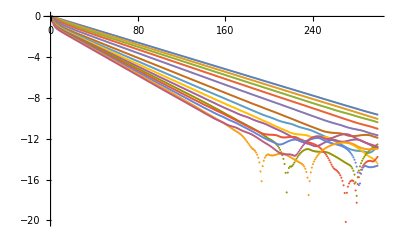

```mathematica
ListPlot[{LogST[[1]],LogST[[2]],LogST[[3]],LogST[[4]],LogST[[5]],LogST[[6]],LogST[[7]],LogST[[8]],LogST[[9]],LogST[[10]],LogST[[11]],LogST[[12]],LogST[[13]],LogST[[14]]}]
```

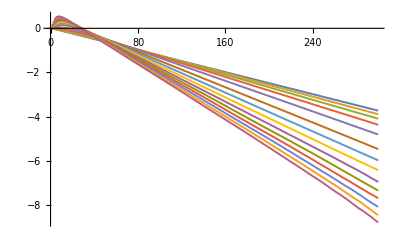

```mathematica
ListPlot[{LogST[[1]],LogST[[2]],LogST[[3]],LogST[[4]],LogST[[5]],LogST[[6]],LogST[[7]],LogST[[8]],LogST[[9]],LogST[[10]],LogST[[11]],LogST[[12]],LogST[[13]],LogST[[14]]}]
```

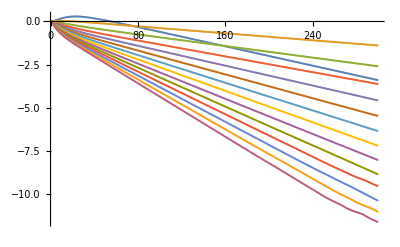

```mathematica
ListPlot[{LogST[[1]],LogST[[2]],LogST[[3]],LogST[[4]],LogST[[5]],LogST[[6]],LogST[[7]],LogST[[8]],LogST[[9]],LogST[[10]],LogST[[11]],LogST[[12]],LogST[[13]],LogST[[14]]}]
```

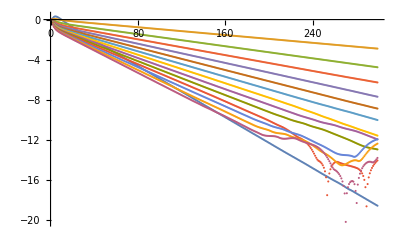

```mathematica
ListPlot[{LogST[[1]],LogST[[2]],LogST[[3]],LogST[[4]],LogST[[5]],LogST[[6]],LogST[[7]],LogST[[8]],LogST[[9]],LogST[[10]],LogST[[11]],LogST[[12]],LogST[[13]],LogST[[14]]}]
```

```mathematica
LogFit=LogST[[6]];
```

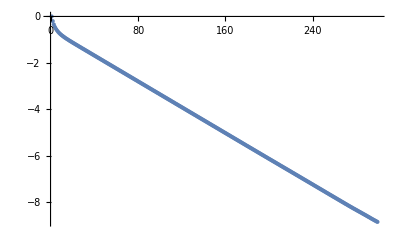

```mathematica
ListPlot[LogFit]
```

```mathematica
bestFitSlope[data_]:=Module[{lm,x},lm=LinearModelFit[data,{1,x},x];
First@Pick[lm["BestFitParameters"],lm["BasisFunctions"],x]];
```

```mathematica
For[m=1,m<Norm[Dimensions@BetaValues+1],m++,
For[n=1,n<Norm[Dimensions@AlphaValues+1],n++,
α=AlphaValues[[n]];
β=BetaValues[[m]];
A=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Electron Transfer\\ST_Theta_"<>ToString[θ]<>"_SolvationPhase_Alpha_"<>ToString[α]<>"_Beta_"<>ToString[β]<>"_x"<>ToString[xzero]<>".csv"];

For[i=1,i<time,i++,
ST[[i]]=Norm[A[[i]]]/Norm[A[[1]]];
];

For[i=1,i<time,i++,
LogST[[i,1]]=ti[[i]];
LogST[[i,2]]=Log[ST[[i]]];
];

Slope[[n+4,m]]=bestFitSlope[LogST]
]
]
```

```mathematica
ArrayPlot[Slope,Mesh-> All, ColorFunction->"Rainbow",PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
ListPlot3D[Slope]
```

-Graphics3D-

```mathematica
fit=ConstantArray[0,{14,2}];
```

```mathematica
For[i=1,i<15,i++,
fit[[i,1]]=AlphaValues[[i]];
fit[[i,2]]=Slope[[i,3]];
]
```

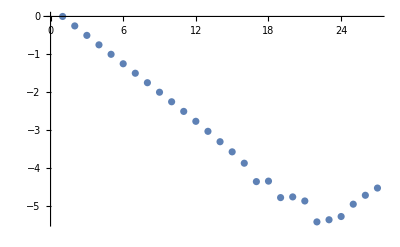

```mathematica
ListPlot[Slope[[1]]]
```

```mathematica
bestFitSlope[fit]
```

-1.02394

```mathematica
bestFitSlope[fit]
```

-0.116736

```mathematica
Plot3D[{-1.x-.11y},{x,0,10},{y,0,10}]
```

-Graphics3D-